```mathematica
model = a*x^b ;
```

```mathematica
{{data = Import["E:\\Alessio\\Desktop\\Computazionale\\es10\\data.txt","Table"]}, {}};
```

```mathematica
M1 = Take[data,-80][[All, {1,2}]];
M2 = Take[data,-80][[All, {1,3}]];
M3 = Take[data,-80][[All, {1,4}]];
H1 = Take[data,-80][[All, {1,5}]];
H2 = Take[data,-80][[All, {1,6}]];
H3 = Take[data,-80][[All, {1,7}]];
SM1 = Take[data,-80][[All, {1,8}]];
SM2 = Take[data,-80][[All, {1,9}]];
SM3 = Take[data,-80][[All, {1,10}]];
SH1 = Take[data,-80][[All, {1,11}]];
SH2 = Take[data,-80][[All, {1,12}]];
SH3 = Take[data,-80][[All, {1,13}]];
```

```mathematica
monte=FindFit[SM1, model,{a,b,c},x,MaxIterations->1000]
hit=FindFit[SH1, model,{a,b,c},x,MaxIterations->1000]
```

{a→773.7,b→-0.494534,c→1.}

{a→1145.81,b→-0.499795,c→1.}

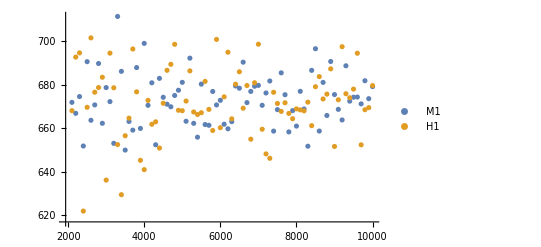

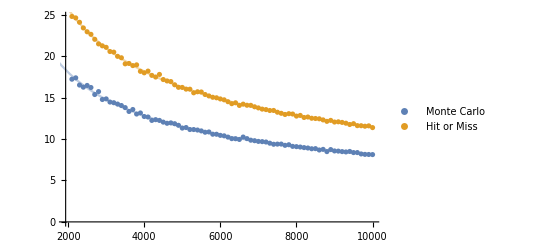

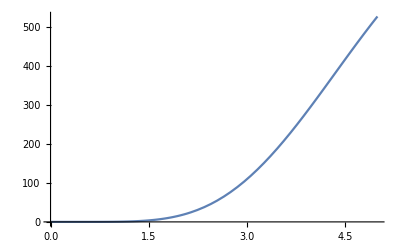

672.193

```mathematica
ListPlot[{M1,H1}, PlotLegends->{ "M1","H1"}, PlotRange->All]
Show[{ListPlot[{SM1,SH1}, PlotLegends->{ "Monte Carlo","Hit or Miss"}, PlotRange->Automatic],Plot[{model/.monte,model/.hit},{x,0,10000},PlotStyle->Opacity[0.4]]}]
Plot[x^7 * Exp[-x],{x,0,5}]
Integrate[x^7 * Exp[-x],{x,0,5}];
N[%]
```

```mathematica
monte=FindFit[SM2, model,{a,b,c},x,MaxIterations->1000]
hit=FindFit[SH2, model,{a,b,c},x,MaxIterations->1000]
```

{a→1844.04,b→-0.500733,c→1.}

{a→2844.3,b→-0.495038,c→1.}

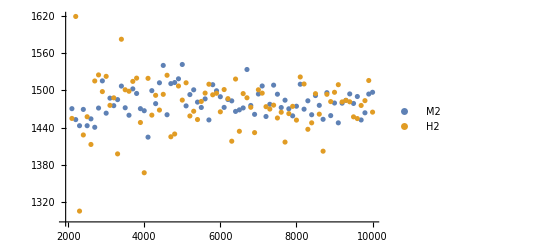

```mathematica
ListPlot[{M2,H2}, PlotLegends->{ "M2","H2"}, PlotRange->All]
```

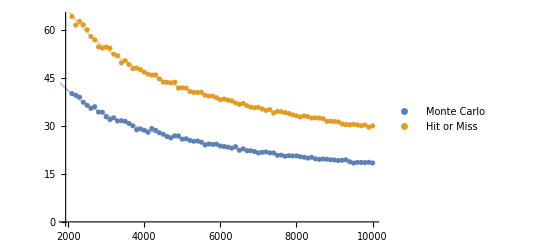

```mathematica
Show[{ListPlot[{SM2,SH2}, PlotLegends->{ "Monte Carlo","Hit or Miss"}, PlotRange->Automatic],Plot[{model/.monte,model/.hit},{x,0,10000},PlotStyle->Opacity[0.4]]}]
```

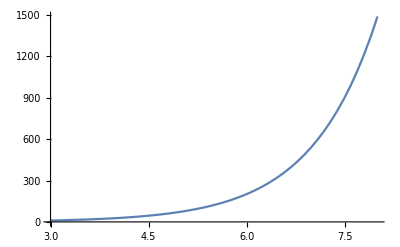

1480.46

```mathematica
Plot[Cosh[x],{x,3,8}]
Integrate[Cosh[x],{x,3,8}];
N[%]
```

```mathematica
monte=FindFit[SM3, model,{a,b,c},x,MaxIterations->1000]
hit=FindFit[SH3, model,{a,b,c},x,MaxIterations->1000]
```

{a→168.77,b→-0.498576,c→1.}

{a→275.821,b→-0.500475,c→1.}

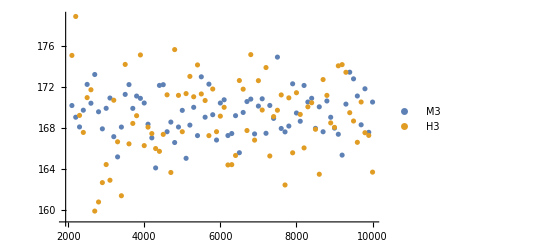

```mathematica
ListPlot[{M3,H3}, PlotLegends->{ "M3","H3"}, PlotRange->All]
```

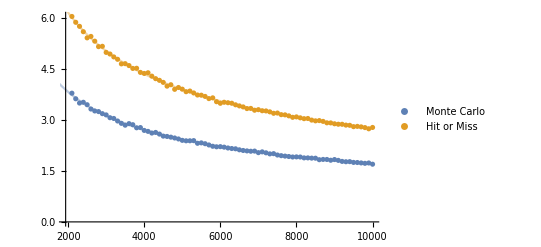

```mathematica
Show[{ListPlot[{SM3,SH3}, PlotLegends->{ "Monte Carlo","Hit or Miss"}, PlotRange->Automatic],Plot[{model/.monte,model/.hit},{x,0,10000},PlotStyle->Opacity[0.4]]}]
```

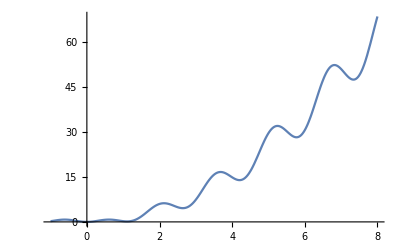

169.482

```mathematica
Plot[x^2 + x*Sin[4x],{x,-1,8}]
Integrate[x^2 + x*Sin[4x],{x,-1,8}];
N[%]
```